## ChooseTmat.nb: Various elastic maps to choose from. First run common_funs.nb

#### NOTES: To derive the symmetry group and display a lattice diagram, run DeriveSymGp[Tmat] To plot an alpha sphere, use cpMONO (see example below). The units of the measured elastic maps are GPa = 10^9 Pa = 10^9 N/m2. The units of density is kg/m3. Sets of elastic maps are defined at the bottom. See also ChooseTmat_pert.nb and ChooseTmat_all.nb

## Override the defaults in common_funs.nb.

```mathematica
(*MinimizationFacts[Tmat_,Σ_]:=OutputFor[Tmat,Σ]*)
```

#### We will rarely need to run Nminimize more than once.

```mathematica
nRuns=1;
```

#### do not display MatrixNote if it is not defined for Tmat

```mathematica
PrintMatrixNote[Tmat_]:=If[MatrixNote[Tmat]!=99,MatrixNote[Tmat]];
```

## User choices

```mathematica
(*Clear[contoursMONO,MaxForScaling]*)
```

#### paths for inputting and outputting files assumes your working directory is called mma and accessible (or linked) from your home directory

```mathematica
currentDirectory=Directory[];
mdir=FileNameJoin[{currentDirectory,"mma"}];
mdir="/Users/carltape/mma/elasticity"
```

#### term used for displaying the map below the lattice diagram

```mathematica
denominator=1;
```

#### default density (this is PREM in the lower crust)

```mathematica
density[Tmat_]:=2900;
```

#### colors for each symmetry class

```mathematica
(*hueGreen=Hue[.5,1,.7];*)
hueGray=GrayLevel[.6];
hueBlue=ColorData["TemperatureMap"][.05];
hueGreen=Hue[.4,1,.8];
HueOfΣ[TRIV]=Gray;
HueOfΣ[MONO]=Black;
HueOfΣ[ORTH]=Purple;
HueOfΣ[TET]  =Blue;
HueOfΣ[CUBE]=Orange;
HueOfΣ[XISO]=hueGreen;
HueOfΣ[ISO]  =Red;
HueOfΣ[TRIG]=Cyan;
```

```mathematica
BetaText[TRIV]="β_TRIV";
BetaText[MONO]="β_MONO";
BetaText[ORTH]="β_ORTH";
BetaText[TET]  ="β_TET";
BetaText[CUBE]="β_CUBE";
BetaText[XISO]="β_XISO";
BetaText[ISO]   ="β_ISO";
BetaText[TRIG] ="β_TRIG";
```

```mathematica
dText[TRIV]="d_TRIV";
dText[MONO]="d_MONO";
dText[ORTH]="d_ORTH";
dText[TET]  ="d_TET";
dText[CUBE]="d_CUBE";
dText[XISO]="d_XISO";
dText[ISO]   ="d_ISO";
dText[TRIG] ="d_TRIG";
```

#### custom histogram

```mathematica
PlotHist[vals_,xlab_,stlab_:"",vbin_:Automatic]:=
Histogram[vals,vbin,"Count",AxesLabel->{None,None},ImageSize->400,Frame->True,FrameLabel->{Style[xlab,FontSize->14,Black],Style["Counts [" <> ToString[Length[vals]]<>"]",FontSize->14,Black]},FrameTicks->{Automatic,Automatic},FrameStyle->Black,LabelStyle->Directive[Black,FontSize->14],PlotTheme->"Detailed",PlotLabel->Style[stlab,FontSize->14,Black]]
```

#### potentially useful title for histogram

```mathematica
stMeanMed[f_,numdig_:2]:=StringJoin["Mean: ",ToString[sfmt[Mean[f],numdig]]," ± ",ToString[sfmt[StandardDeviation[f],numdig]]," Median: ",ToString[sfmt[Median[f],numdig]]," ± ",ToString[sfmt[MedianDeviation[f],numdig]]];
```

#### plotting options for balls

```mathematica
plotpoints=10;
```

```mathematica
plotpoints=Automatic;
```

```mathematica
contourstyle=Thickness[0.002];
```

```mathematica
contourstyle=Automatic;
```

```mathematica
eyerad=50;
```

```mathematica
eye0=eyerad xyzTP[{30Degree,65Degree}];
```

```mathematica
eye=eye0;
```

```mathematica
options:={ViewPoint->eye,Lighting->{{"Ambient",White}},Boxed->False};
```

```mathematica
ShiftToEye=.04;
AngRadDisk=2.Degree;
tknsForGC=.008;  (* thickness of the green great circle on the XISO spheres *)
```

```mathematica
TwoCol=Green;
ThreeCol=Black;
FourCol=Magenta;
```

```mathematica
TwoRad=1.25AngRadDisk;
ThreeRad=1.5AngRadDisk;
FourRad=0.5 TwoRad;
```

```mathematica
Bradius=1;
Bcenter={0,0,0};
```

#### use the 7-argument version of TwoFoldGraphics

```mathematica
AllFoldGraphics[Σ_,U_,ShiftToEye_,eye_]:={
TwoFoldGraphics[Σ,U,TwoRad,ShiftToEye,eye,tknsForGC,TwoCol],
ThreeFoldGraphics[Σ,U,ThreeRad,ShiftToEye,eye,tknsForGC,ThreeCol],
FourFoldGraphics[Σ,U,FourRad,ShiftToEye,eye,tknsForGC,FourCol]
}
```

```mathematica
TwoFoldGraphicsText[Σ_,U_,TwoRad_,ShiftToEye_,eye_,tknsForGC_,TwoCol_]:=Module[{},
Print["Σ = ",Σ];
Print["U = ",DispMat[U,4]];
Print["TwoRad = ",TwoRad];
Print["ShiftToEye = ",ShiftToEye];
Print["eye = ",eye];
Print["tknsForGC = ",tknsForGC];
Print["TwoCol = ",TwoCol];]
```

#### axes options for the balls

```mathematica
lengthAxis=1.35;
BBrad=1;
ArrowScale=0.17;
tkns=0.009;
```

#### add tiny points so that the ball is always centered within the inset plot

```mathematica
ptsz=0.001;
basepts={{1,0,0},{-1,0,0},{0,1,0},{0,-1,0},{0,0,1},{0,0,-1}};
(*basepts=SpherePoints[100];*)
extrapts=1.01 lengthAxis basepts;
```

#### gray arrows for coordinate axes (ArrowColor is some Hue, but only relevant if WantArrowColor = “Custom”.) note: as written, this does NOT get reevaluated when it is called (= not :=)

```mathematica
PaxesForLattice={Paxes[True,True,True,id,{0,0,0},lengthAxis,BBrad,ArrowScale,tkns,"Gray",ArrowColor],{PointSize[ptsz],Point/@extrapts}};
```

#### calculate t-value just prior to an eigenvalue reaching zero

```mathematica
Tpert[Tmat_,t_]:=(1-t) Tmat+t Closest[Tmat,ISO];
```

```mathematica
Clear[tpertTmatAux]
tpertTmatAux[Tmat_,dt_,tstart_,tend_]:=Module[{t=tstart,eigs,step=If[tstart<tend,dt,-dt]},While[(step>0&&t<=tend)||(step<0&&t>=tend),eigs=Eigenvalues[Tpert[Tmat,t]];
(*Print["t: ",t," | Eigenvalues: ",eigs];*)
If[Min[eigs]<=0,Return[t-step];];
t+=step;];
Print["No eigenvalue hit zero within the given range."];
None];
tpertTmat[Tmat_,dt_:0.01,tstart_:0,tend_:-100]:=tpertTmatAux[Tmat,dt,tstart,tend];
```

## Functions for displaying output

#### round number to 0.01

```mathematica
sfmt[num_,numdig_:2]:=NumberForm[num,{Infinity,numdig}]
```

#### display a nicely formatted matrix (mostly used for insets in figures) number of digits: numdig=1 means 0.1, numdig=2 means 0.01

```mathematica
(* DispMat[Tmat_,numdig_]:=MatrixForm[Map[PaddedForm[Chop[#,0.00001],{Infinity,numdig},NumberPadding->{"","0"}]&,Tmat,{2}],TableAlignments->Right]; *)
```

```mathematica
(* DispMat[Tmat_,numdig_]:=Module[{isSymbolicOrIntegerMatrix},isSymbolicOrIntegerMatrix=AllTrue[Flatten[Tmat],#===Round[#]&];
MatrixForm[If[isSymbolicOrIntegerMatrix,Tmat,Map[PaddedForm[Chop[#,0.00001],{Infinity,numdig},NumberPadding->{"","0"}]&,Tmat,{2}]],TableAlignments->Right]]; *)
```

```mathematica
DispMat[input_,numdig_:2]:=Module[{isSymbolicOrInteger,formattedInput},isSymbolicOrInteger=AllTrue[Flatten[input],#===Round[#]&];
formattedInput=If[isSymbolicOrInteger,input,Map[PaddedForm[Chop[#,0.00001],{Infinity,numdig},NumberPadding->{"","0"}]&,input,{Depth[input]-1}]];
MatrixForm[If[VectorQ[input],{formattedInput}ᵀ,formattedInput],TableAlignments->Right]];
```

```mathematica
DispMat[{1.34,12.4,121.2}]
DispMat[{1.34,12.4,121.2},1]
```

#### display Tmat (BB basis) and corresponding Cmat (Voigt) (note: might want to add an argument to list decimal output instead of exact expressions)

```mathematica
PrintVoigt[Tmat_]:=(
Print["The [T]_𝔹𝔹 matrix is ",MatrixForm[Chop[Tmat,0.0001]]]; 
(*Print["The [T]_𝔹𝔹 matrix is ",DispMat[Tmat,2]];*)
Print["The eigenvalues are: ",Eigenvalues[Tmat] ]; 
(*Print["The eigenvalues are: ",1.Eigenvalues[Tmat]];*)
Print["The Voigt matrix is ",MatrixForm[Chop[Simplify[CmatOfTmat[Tmat]],0.0001]]];
(*Print["The Voigt matrix is ",DispMat[Simplify[CmatOfTmat[Tmat]],2]];*)
MinimizationFacts[Tmat,ISO];
(*OutputFor[Tmat,ISO];*)
(*TmatISO=Closest[Tmat,ISO];*)
)
```

#### nm1 --> 1, nm2 --> 2, etc

```mathematica
TextNM[nm_]:=StringTake[ToString[nm],-1]
```

#### Symbol used in the lattice of node maps (K is for the closest-Sigma elastic map)

```mathematica
SymNM[nm_]:=If[nm===nm2,"K","S"]
```

#### simple text label for custom Tmat

```mathematica
Tlab[Tmat_]:=StringSplit[MatrixNote[Tmat]][[3]]
```

#### display the maps (the 1.Tmat will ensure numerical entries are displayed for all maps) example syntax: TmatTable[{Tmat1, Tmat2, Tmat3}]

```mathematica
TmatTable[Tmatall_,numdig_:2]:=TableForm[Prepend[Flatten[Table[{{Tlab[Tmat],MatrixShortNote[Tmat],1.βT[Tmat,ISO]/Degree,DispMat[1.Tmat,numdig]},{Spacer[0],Spacer[0],Spacer[0],Spacer[1]}},{Tmat,Tmatall}],1],{ToString[Length[Tmatall]]<>" elastic maps","","",""}]]
```

## CHOOSE ONE OF THE FOLLOWING ELASTIC MAPS (e.g., Tmat = TmatBrownAn00)

## Brown, Angel, Ross (2016) maps (Table 2)

#### Table 2, column An00 (pure albite)

```mathematica
CmatBrownAn00=({{68.3, 32.2, 30.4, 4.9, -2.3, -0.9}, {32.2, 184.3, 5., -4.4, -7.8, -6.4}, {30.4, 5., 180., -9.2, 7.5, -9.4}, {4.9, -4.4, -9.2, 25., -2.4, -7.2}, {-2.3, -7.8, 7.5, -2.4, 26.9, 0.6}, {-0.9, -6.4, -9.4, -7.2, 0.6, 33.6}});
TmatBrownAn00 = TmatOfCmat[CmatBrownAn00];
MatrixNote[TmatBrownAn00]="T is BrownAn00"
MatrixShortNote[TmatBrownAn00]="An00"
PrintVoigt[TmatBrownAn00]
density[TmatBrownAn00]=2623;
```

#### original commands for specifying contours manually

```mathematica
(*cmin=0;cmax=24; dc=2;
contoursMONO[TmatBrownAn00]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAn00]=cmax-dc;*)
```

## Optional interlude: plotting alpha spheres

```mathematica
ExamplePlots = False;
```

#### alphaMONO sphere plot note: set plotpoints=50 if you want to see the smallest contours (which may disappear when rotating the sphere)

```mathematica
If[ExamplePlots,(
Tex=TmatBrownAn00;
Print[contours[Tex,MONO]];
Print[MaxForScaling[Tex,MONO]];
Show[cpMONO[Tex,contours[Tex,MONO],MaxForScaling[Tex,MONO],plotpoints,contourstyle],options]
)]
```

#### alphaMONO sphere plot - with coordinate axes

```mathematica
If[ExamplePlots,Show[{cpMONO[Tex,contours[Tex,MONO],MaxForScaling[Tex,MONO],plotpoints,contourstyle],Graphics3D[PaxesForLattice]},options]]
```

#### alphaMONO sphere plot - with coordinate axes and colored dots

```mathematica
If[ExamplePlots,(
Σ=CUBE;
Uex=UT[Tex,Σ];
Print[TwoFoldGraphicsText[Σ,Uex,TwoRad,ShiftToEye,eye,tknsForGC,TwoCol]];
Show[{cpMONO[Closest[Tex,Σ],contours[Tex,MONO],MaxForScaling[Tex,MONO],plotpoints,contourstyle],Graphics3D[{PaxesForLattice,AllFoldGraphics[Σ,Uex,ShiftToEye,eye]}]},options]
)]
```

#### alphaMONO sphere plot - with coordinate axes, colored U axes, and colored dots (red = u1, blue=u2, yellow=u3)

```mathematica
If[ExamplePlots,(
PaxesForLatticeU[U_]:={Paxes[True,True,True,U,{0,0,0},lengthAxis,BBrad,ArrowScale,tkns,"TriColor",ArrowColor],{PointSize[ptsz],Point/@extrapts}};
Show[{cpMONO[Closest[Tex,Σ],contours[Tex,MONO],MaxForScaling[Tex,MONO],plotpoints,contourstyle],Graphics3D[{PaxesForLattice,PaxesForLatticeU[Uex],
AllFoldGraphics[Σ,Uex,ShiftToEye,eye]}]},options]
)]
```

#### Example rotation: rotate the original map by a specified angle about a specified axis. Here we choose to rotate the map about the u2 (blue) axis by 30 deg.

```mathematica
If[ExamplePlots,(
ξex=30Degree;
Urot=ROT[ξex,Uex.{0,1,0}];
Texrot=Conj[Tex,Urot];
GraphicsRow[{Show[{cpMONO[Tex,contours[Tex,MONO],MaxForScaling[Tex,MONO],plotpoints,contourstyle],Graphics3D[{PaxesForLattice,PaxesForLatticeU[Uex]}]},options],Show[{cpMONO[Texrot,contours[Tex,MONO],MaxForScaling[Tex,MONO],plotpoints,contourstyle],Graphics3D[{PaxesForLattice,PaxesForLatticeU[Uex]}]},options]}]
)]
```

#### Another example: rotate the map about the u1 (red) axis by 30 deg.

```mathematica
If[ExamplePlots,(
Urot=ROT[ξex,Uex.{1,0,0}];
Texrot=Conj[Tex,Urot];
GraphicsRow[{Show[{cpMONO[Tex,contours[Tex,MONO],MaxForScaling[Tex,MONO],plotpoints,contourstyle],Graphics3D[{PaxesForLattice,PaxesForLatticeU[Uex]}]},options],Show[{cpMONO[Texrot,contours[Tex,MONO],MaxForScaling[Tex,MONO],plotpoints,contourstyle],Graphics3D[{PaxesForLattice,PaxesForLatticeU[Uex]}]},options]}]
)]
```

## Resume BrownAn00

#### rotation matrix from MSAT MS_axes()

```mathematica
RfromMSATBrownAn00=({{0.990296658297612, 0.133516610230907, 0.038546638725448}, {0.102569961991151, -0.515083832840562, -0.850980639053210}, {-0.093765299880691, 0.846677010399317, -0.523780592041705}}); 
UfromMSATBrownAn00 =Transpose[RfromMSATBrownAn00];
```

```mathematica
RfromMSATBrownAn00STIFF=({{0.130978233503532, -0.850789836626075, 0.508921758467911}, {-0.131215510186955, 0.493950618751117, 0.859532009945974}, {-0.982663315807948, -0.179358412485073, -0.046940042992768}}); 
UfromMSATBrownAn00STIFF =Transpose[RfromMSATBrownAn00STIFF];
```

#### lattice diagram: DeriveSymGp[TmatBrownAn00]

```mathematica
(*DeriveSymGp[TmatBrownAn00]*)
```

#### BrownAn00 perturbed to its extreme

```mathematica
(*Tmat1=TmatBrownAn00;
Tmat2=Closest[TmatBrownAn00,ISO];
t1=-tpert[TmatBrownAn00];
TmatBrownAn00Pert=(1-t1) Tmat1+t1 Tmat2;*)
TmatBrownAn00Pert=Tpert[TmatBrownAn00,tpertTmat[TmatBrownAn00]+0.01];
```

```mathematica
MatrixNote[TmatBrownAn00Pert]="T is BrownAn00Pert"
MatrixShortNote[TmatBrownAn00Pert]="An00p"
PrintVoigt[TmatBrownAn00Pert]
density[TmatBrownAn00Pert]=density[TmatBrownAn00];
```

```mathematica
(*cmin=0;cmax=36; dc=3;
contoursMONO[TmatBrownAn00Pert]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAn00Pert]=cmax-dc;*)
```

#### Table 2, column An25

```mathematica
CmatBrownAn25=({{87.1, 43.9, 35.4, 6.1, -0.4, -0.6}, {43.9, 174.9, 18., -5.9, -2.9, -6.5}, {35.4, 18., 166.1, -2.9, 4.6, -10.7}, {6.1, -5.9, -2.9, 22.9, -1.3, -5.2}, {-0.4, -2.9, 4.6, -1.3, 29., 0.8}, {-0.6, -6.5, -10.7, -5.2, 0.8, 35.}});
TmatBrownAn25 = TmatOfCmat[CmatBrownAn25];
MatrixNote[TmatBrownAn25]="T is BrownAn25"
MatrixShortNote[TmatBrownAn25]="An25"
PrintVoigt[TmatBrownAn25]
density[TmatBrownAn25]=2653;
```

```mathematica
(*cmin=0;cmax=18; dc=2;
contoursMONO[TmatBrownAn25]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAn25]=cmax-dc;*)
```

#### Table 2, column An37

```mathematica
CmatBrownAn37=({{96.2, 46.1, 38.4, 5.9, -0.2, -0.4}, {46.1, 189.4, 15.4, -7., -5.1, -6.8}, {38.4, 15.4, 171.9, 2.2, 7.2, -9.8}, {5.9, -7., 2.2, 23.6, -1.1, -4.8}, {-0.2, -5.1, 7.2, -1.1, 33.1, 1.4}, {-0.4, -6.8, -9.8, -4.8, 1.4, 35.5}});
TmatBrownAn37 = TmatOfCmat[CmatBrownAn37];
MatrixNote[TmatBrownAn37]="T is BrownAn37"
MatrixShortNote[TmatBrownAn37]="An37"
PrintVoigt[TmatBrownAn37]
density[TmatBrownAn37]=2666;
```

```mathematica
(*cmin=0;cmax=18; dc=2;
contoursMONO[TmatBrownAn37]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAn37]=cmax-dc;*)
```

#### Table 2, column An48

```mathematica
CmatBrownAn48=({{104.6, 51.5, 43.9, 6.5, 0.1, -0.8}, {51.5, 201.4, 14.5, -2.4, -4.8, -9.9}, {43.9, 14.5, 172.8, -0.4, 6.9, -5.7}, {6.5, -2.4, -0.4, 22.9, -1., -3.8}, {0.1, -4.8, 6.9, -1., 33., 2.1}, {-0.8, -9.9, -5.7, -3.8, 2.1, 35.6}});
TmatBrownAn48 = TmatOfCmat[CmatBrownAn48];
MatrixNote[TmatBrownAn48]="T is BrownAn48"
MatrixShortNote[TmatBrownAn48]="An48"
PrintVoigt[TmatBrownAn48]
density[TmatBrownAn48]=2683;
```

```mathematica
(*cmin=0;cmax=18; dc=2;
contoursMONO[TmatBrownAn48]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAn48]=cmax-dc;*)
```

#### Table 2, column An60

```mathematica
CmatBrownAn60=({{109.3, 53.1, 42.1, 7.6, 1.2, -7.7}, {53.1, 185.5, 21.9, -2.9, 0.7, -6.8}, {42.1, 21.9, 164.1, 0.2, 2.5, 0.7}, {7.6, -2.9, 0.2, 22.2, 0.2, 1.4}, {1.2, 0.7, 2.5, 0.2, 33.1, 2.8}, {-7.7, -6.8, 0.7, 1.4, 2.8, 36.8}});
TmatBrownAn60 = TmatOfCmat[CmatBrownAn60];
MatrixNote[TmatBrownAn60]="T is BrownAn60"
MatrixShortNote[TmatBrownAn60]="An60"
PrintVoigt[TmatBrownAn60]
density[TmatBrownAn60]=2702;
```

```mathematica
(*cmin=0;cmax=16; dc=2;
contoursMONO[TmatBrownAn60]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAn60]=cmax-dc;*)
```

#### Table 2, column An67

```mathematica
CmatBrownAn67=({{120.3, 54.4, 40.8, 9.2, 2.3, -10.1}, {54.4, 193.5, 16.1, 0.9, 3.1, -2.9}, {40.8, 16.1, 171.9, -0.9, 2.2, -0.3}, {9.2, 0.9, -0.9, 24., 0.7, 0.3}, {2.3, 3.1, 2.2, 0.7, 35.5, 3.2}, {-10.1, -2.9, -0.3, 0.3, 3.2, 37.3}});
TmatBrownAn67 = TmatOfCmat[CmatBrownAn67];
MatrixNote[TmatBrownAn67]="T is BrownAn67"
MatrixShortNote[TmatBrownAn67]="An67"
PrintVoigt[TmatBrownAn67]
density[TmatBrownAn67]=2721;
```

```mathematica
(*cmin=0;cmax=18; dc=2;
contoursMONO[TmatBrownAn67]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAn67]=cmax-dc;*)
```

#### Table 2, column An78

```mathematica
CmatBrownAn78=({{120.4, 56.6, 49.9, 9., 3.2, -3.}, {56.6, 191.6, 26.3, 2.1, 5.4, -9.9}, {49.9, 26.3, 163.7, 1.7, 1.7, -8.1}, {9., 2.1, 1.7, 23.3, 0.8, 0.9}, {3.2, 5.4, 1.7, 0.8, 32.8, 4.5}, {-3., -9.9, -8.1, 0.9, 4.5, 35.}});
TmatBrownAn78 = TmatOfCmat[CmatBrownAn78];
MatrixNote[TmatBrownAn78]="T is BrownAn78"
MatrixShortNote[TmatBrownAn78]="An78"
PrintVoigt[TmatBrownAn78]
density[TmatBrownAn78]=2725;
```

```mathematica
(*cmin=0;cmax=16; dc=2;
contoursMONO[TmatBrownAn78]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAn78]=cmax-dc;*)
```

#### Table 2, column An96

```mathematica
CmatBrownAn96=({{132.2, 64., 55.3, 9.5, 5.1, -10.8}, {64., 200.2, 31.9, 7.5, 3.5, -7.2}, {55.3, 31.9, 163.9, 6.6, 0.5, 1.6}, {9.5, 7.5, 6.6, 24.6, 3., -2.2}, {5.1, 3.5, 0.5, 3., 36.6, 5.2}, {-10.8, -7.2, 1.6, -2.2, 5.2, 36.}});
TmatBrownAn96 = TmatOfCmat[CmatBrownAn96];
MatrixNote[TmatBrownAn96]="T is BrownAn96"
MatrixShortNote[TmatBrownAn96]="An96"
PrintVoigt[TmatBrownAn96]
density[TmatBrownAn96]=2757;
```

```mathematica
(*cmin=0;cmax=16; dc=2;
contoursMONO[TmatBrownAn96]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAn96]=cmax-dc;*)
```

## Brown and Abramson (2016) maps

#### Table 3, Sample 1

```mathematica
CmatBrownAbramson2016s1=({{119.2, 47.5, 41.2, 0, -1.7, 0}, {47.5, 182.2, 58.2, 0, -5.6, 0}, {41.2, 58.2, 228.0, 0, -30.6, 0}, {0, 0, 0, 75.6, 0, 4.7}, {-1.7, -5.6, -30.6, 0, 45.9, 0}, {0, 0, 0, 4.7, 0, 49.2}});
TmatBrownAbramson2016s1= TmatOfCmat[CmatBrownAbramson2016s1];
MatrixNote[TmatBrownAbramson2016s1]="T is BrownAbramson1"
MatrixShortNote[TmatBrownAbramson2016s1]="BA1"
PrintVoigt[TmatBrownAbramson2016s1]
density[TmatBrownAbramson2016s1]=3027;
```

```mathematica
(*cmin=0;cmax=16; dc=2;
contoursMONO[TmatBrownAbramson2016s1]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAbramson2016s1]=cmax-dc;*)
```

#### rotation matrix from MSAT MS_axes()

```mathematica
RfromMSATBrownAbramson2016s1=({{0.971758767912463, 0, 0.235976475491204}, {0, 1, 0}, {-0.235976475491204, 0, 0.971758767912464}}); 
UfromMSATBrownAbramson2016s1 =Transpose[RfromMSATBrownAbramson2016s1];
```

#### Table 3, Sample 2

```mathematica
CmatBrownAbramson2016s2=({{122.7, 50.0, 44.3, 0, -1.4, 0}, {50.0, 184.6, 59.5, 0, -7.1, 0}, {44.3, 59.5, 223.7, 0, -29.4, 0}, {0, 0, 0, 70.5, 0, 5.3}, {-1.4, -7.1, -29.4, 0, 42.5, 0}, {0, 0, 0, 5.3, 0, 45.9}});
TmatBrownAbramson2016s2= TmatOfCmat[CmatBrownAbramson2016s2];
MatrixNote[TmatBrownAbramson2016s2]="T is BrownAbramson2"
MatrixShortNote[TmatBrownAbramson2016s2]="BA2"
PrintVoigt[TmatBrownAbramson2016s2]
density[TmatBrownAbramson2016s2]=3255;
```

```mathematica
(*cmin=0;cmax=14; dc=2;
contoursMONO[TmatBrownAbramson2016s2]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAbramson2016s2]=cmax-dc;*)
```

#### Table 3, Sample 3

```mathematica
CmatBrownAbramson2016s3=({{133.6, 50.9, 43.1, 0, -0.8, 0}, {50.9, 193.4, 58.3, 0, -10.8, 0}, {43.1, 58.3, 225.8, 0, -30.3, 0}, {0, 0, 0, 75.5, 0, 3.8}, {-0.8, -10.8, -30.3, 0, 47.5, 0}, {0, 0, 0, 3.8, 0, 50.4}});
TmatBrownAbramson2016s3= TmatOfCmat[CmatBrownAbramson2016s3];
MatrixNote[TmatBrownAbramson2016s3]="T is BrownAbramson3"
MatrixShortNote[TmatBrownAbramson2016s3]="BA3"
PrintVoigt[TmatBrownAbramson2016s3]
density[TmatBrownAbramson2016s3]=3162;
```

```mathematica
(*cmin=0;cmax=14; dc=2;
contoursMONO[TmatBrownAbramson2016s3]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAbramson2016s3]=cmax-dc;*)
```

#### Table 3, Sample 4

```mathematica
CmatBrownAbramson2016s4=({{122.8, 51.8, 45.9, 0, -0.7, 0}, {51.8, 189.3, 62.3, 0, -7.0, 0}, {45.9, 62.3, 222.9, 0, -30.0, 0}, {0, 0, 0, 71.5, 0, 5.4}, {-0.7, -7.0, -30.0, 0, 46.8, 0}, {0, 0, 0, 5.4, 0, 46.2}});
TmatBrownAbramson2016s4= TmatOfCmat[CmatBrownAbramson2016s4];
MatrixNote[TmatBrownAbramson2016s4]="T is BrownAbramson4"
MatrixShortNote[TmatBrownAbramson2016s4]="BA4"
PrintVoigt[TmatBrownAbramson2016s4]
density[TmatBrownAbramson2016s4]=3293;
```

```mathematica
(*cmin=0;cmax=14; dc=2;
contoursMONO[TmatBrownAbramson2016s4]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAbramson2016s4]=cmax-dc;*)
```

#### Table 3, Sample 5

```mathematica
CmatBrownAbramson2016s5=({{108.6, 48.4, 37.7, 0, 1.0, 0}, {48.4, 191.6, 59.2, 0, -5.6, 0}, {37.7, 59.2, 230.8, 0, -29.6, 0}, {0, 0, 0, 77.0, 0, 7.9}, {1.0, -5.6, -29.6, 0, 50.0, 0}, {0, 0, 0, 7.9, 0, 48.6}});
TmatBrownAbramson2016s5= TmatOfCmat[CmatBrownAbramson2016s5];
MatrixNote[TmatBrownAbramson2016s5]="T is BrownAbramson5"
MatrixShortNote[TmatBrownAbramson2016s5]="BA5"
PrintVoigt[TmatBrownAbramson2016s5]
density[TmatBrownAbramson2016s5]=3038;
```

```mathematica
(*cmin=0;cmax=16; dc=2;
contoursMONO[TmatBrownAbramson2016s5]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAbramson2016s5]=cmax-dc;*)
```

#### Table 3, Sample 6

```mathematica
CmatBrownAbramson2016s6=({{131.1, 53.2, 47.2, 0, -1.0, 0}, {53.2, 186.6, 60.3, 0, -8.5, 0}, {47.2, 60.3, 224.3, 0, -30.3, 0}, {0, 0, 0, 72.5, 0, 4.4}, {-1.0, -8.5, -30.3, 0, 46.5, 0}, {0, 0, 0, 4.4, 0, 48.0}});
TmatBrownAbramson2016s6= TmatOfCmat[CmatBrownAbramson2016s6];
MatrixNote[TmatBrownAbramson2016s6]="T is BrownAbramson6"
MatrixShortNote[TmatBrownAbramson2016s6]="BA6"
PrintVoigt[TmatBrownAbramson2016s6]
density[TmatBrownAbramson2016s6]=3213;
```

```mathematica
(*cmin=0;cmax=14; dc=2;
contoursMONO[TmatBrownAbramson2016s6]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAbramson2016s6]=cmax-dc;*)
```

#### Table 3, Sample 7

```mathematica
CmatBrownAbramson2016s7=({{122.7, 52.6, 47.5, 0, -2.0, 0}, {52.6, 178.6, 60.8, 0, -9.5, 0}, {47.5, 60.8, 216.6, 0, -31.0, 0}, {0, 0, 0, 67.5, 0, 6.3}, {-2.0, -9.5, -31.0, 0, 39.7, 0}, {0, 0, 0, 6.3, 0, 40.8}});
TmatBrownAbramson2016s7= TmatOfCmat[CmatBrownAbramson2016s7];
MatrixNote[TmatBrownAbramson2016s7]="T is BrownAbramson7"
MatrixShortNote[TmatBrownAbramson2016s7]="BA7"
PrintVoigt[TmatBrownAbramson2016s7]
density[TmatBrownAbramson2016s7]=3418;
```

```mathematica
(*cmin=0;cmax=14; dc=2;
contoursMONO[TmatBrownAbramson2016s7]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAbramson2016s7]=cmax-dc;*)
```

#### Table 3, Sample 8

```mathematica
CmatBrownAbramson2016s8=({{141.6, 57.1, 49.6, 0, -0.2, 0}, {57.1, 197.8, 60.9, 0, -10.9, 0}, {49.6, 60.9, 225.4, 0, -31.4, 0}, {0, 0, 0, 75.8, 0, 3.3}, {-0.2, -10.9, -31.4, 0, 49.9, 0}, {0, 0, 0, 3.3, 0, 51.7}});
TmatBrownAbramson2016s8= TmatOfCmat[CmatBrownAbramson2016s8];
MatrixNote[TmatBrownAbramson2016s8]="T is BrownAbramson8"
MatrixShortNote[TmatBrownAbramson2016s8]="BA8"
PrintVoigt[TmatBrownAbramson2016s8]
density[TmatBrownAbramson2016s8]=3163;
```

```mathematica
(*cmin=0;cmax=12; dc=1;
contoursMONO[TmatBrownAbramson2016s8]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAbramson2016s8]=cmax-dc;*)
```

#### Table 3, Sample 9

```mathematica
CmatBrownAbramson2016s9=({{148.7, 56.5, 48.8, 0, 0.3, 0}, {56.5, 204.6, 61.9, 0, -6.9, 0}, {48.8, 61.9, 232.1, 0, -28.8, 0}, {0, 0, 0, 76.7, 0, 1.9}, {0.3, -6.9, -28.8, 0, 54.1, 0}, {0, 0, 0, 1.9, 0, 52.9}});
TmatBrownAbramson2016s9= TmatOfCmat[CmatBrownAbramson2016s9];
MatrixNote[TmatBrownAbramson2016s9]="T is BrownAbramson9"
MatrixShortNote[TmatBrownAbramson2016s9]="BA9"
PrintVoigt[TmatBrownAbramson2016s9]
density[TmatBrownAbramson2016s9]=3190;
```

```mathematica
(*cmin=0;cmax=11; dc=1;
contoursMONO[TmatBrownAbramson2016s9]=Range[cmin,cmax,dc];
MaxForScaling[TmatBrownAbramson2016s9]=cmax-dc;*)
```

## Aminzadeh et al. (2022) maps

#### Bukov gneiss: Table 3, 0.1 MPa pressure (column 1)

```mathematica
CmatAminzadehBukov0p1=({{89.90, 27.02, 14.85, 0.41, -0.51, -1.06}, {27.02, 78.88, 16.66, 0.05, 3.78, -0.02}, {14.85, 16.66, 45.05, -0.91, -0.55, 3.08}, {0.41, 0.05, -0.91, 19.68, -0.93, -1.66}, {-0.51, 3.78, -0.55, -0.93, 21.79, 1.11}, {-1.06, -0.02, 3.08, -1.66, 1.11, 28.55}});
TmatAminzadehBukov0p1= TmatOfCmat[CmatAminzadehBukov0p1];
MatrixNote[TmatAminzadehBukov0p1]="T is Aminzadeh-Bukov-0.1"
MatrixShortNote[TmatAminzadehBukov0p1]="BUK"
PrintVoigt[TmatAminzadehBukov0p1]
density[TmatAminzadehBukov0p1]=2750;
```

```mathematica
(*cmin=0;cmax=14; dc=2;
contoursMONO[TmatAminzadehBukov0p1]=Range[cmin,cmax,dc];
MaxForScaling[TmatAminzadehBukov0p1]=cmax-dc;*)
```

#### Grimsel granite: Table 4, 0.1 MPa pressure (column 1)

```mathematica
CmatAminzadehGrimsel0p1=({{48.16, 19.34, 13.23, -1.18, 0.06, -0.30}, {19.34, 44.60, 10.81, 0.53, -1.70, 0.43}, {13.23, 10.81, 23.07, -0.29, 0.36, -0.98}, {-1.18, 0.53, -0.29, 10.63, 0.73, 0.85}, {0.06, -1.70, 0.36, 0.73, 7.67, 0.70}, {-0.30, 0.43, -0.98, 0.85, 0.70, 13.85}});
TmatAminzadehGrimsel0p1= TmatOfCmat[CmatAminzadehGrimsel0p1];
MatrixNote[TmatAminzadehGrimsel0p1]="T is Aminzadeh-Grimsel-0.1"
MatrixShortNote[TmatAminzadehGrimsel0p1]="GRM"
PrintVoigt[TmatAminzadehGrimsel0p1]
density[TmatAminzadehGrimsel0p1]=2700;
```

```mathematica
(*cmin=0;cmax=14; dc=2;
contoursMONO[TmatAminzadehGrimsel0p1]=Range[cmin,cmax,dc];
MaxForScaling[TmatAminzadehGrimsel0p1]=cmax-dc;*)
```

## List of maps

#### Browaeys and Chevrot (2004) - olivine

```mathematica
CmatBColivine=1.({{192, 66, 60, 0, 0, 0}, {66, 160, 56, 0, 0, 0}, {60, 56, 272, 0, 0, 0}, {0, 0, 0, 60, 0, 0}, {0, 0, 0, 0, 62, 0}, {0, 0, 0, 0, 0, 49}});
TmatBColivine = TmatOfCmat[CmatBColivine];
MatrixNote[TmatBColivine]="T is BColivine"
MatrixShortNote[TmatBColivine]="BCO"
PrintVoigt[TmatBColivine]
```

```mathematica
(*cmin=0;cmax=11; dc=1;
contoursMONO[TmatBColivine]=Range[cmin,cmax,dc];
MaxForScaling[TmatBColivine]=cmax-dc;*)
```

#### lattice for TmatBColivine: DeriveSymGp[TmatBColivine]

The symmetry classes Σ with β_Σ^T = 0  are {TRIV,MONO,ORTH}  (See the lattice)

The symmetry class for T is therefore ORTH

The symmetry group for T is U 𝕌_ORTH U^T, where U = UT[Tmat,ORTH] = (0 | 1. | 0
-1. | 0 | 0
0 | 0 | 1.)

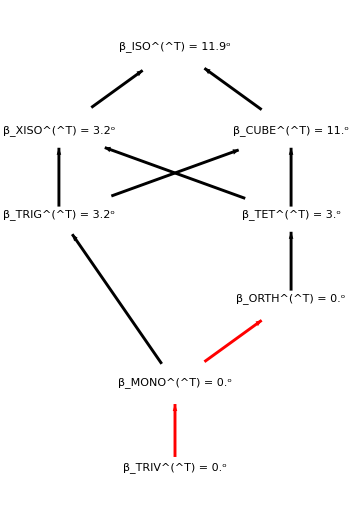

#### Browaeys and Chevrot (2004) - enstatite

```mathematica
CmatBCenstatite=1.({{225, 54, 72, 0, 0, 0}, {54, 214, 53, 0, 0, 0}, {72, 53, 178, 0, 0, 0}, {0, 0, 0, 78, 0, 0}, {0, 0, 0, 0, 82, 0}, {0, 0, 0, 0, 0, 76}});
TmatBCenstatite = TmatOfCmat[CmatBCenstatite];
MatrixNote[TmatBCenstatite]="T is BCenstatite"
MatrixShortNote[TmatBCenstatite]="BCE"
PrintVoigt[TmatBCenstatite]
```

```mathematica
(*cmin=0;cmax=4.5; dc=0.5;
contoursMONO[TmatBCenstatite]=Range[cmin,cmax,dc];
MaxForScaling[TmatBCenstatite]=cmax-dc;*)
```

#### lattice for TmatBCenstatite: DeriveSymGp[TmatBCenstatite]

The symmetry classes Σ with β_Σ^T = 0  are {TRIV,MONO,ORTH}  (See the lattice)

The symmetry class for T is therefore ORTH

The symmetry group for T is U 𝕌_ORTH U^T, where U = UT[Tmat,ORTH] = (-1. | 0 | 0
0 | -1. | 0
0 | 0 | 1.)

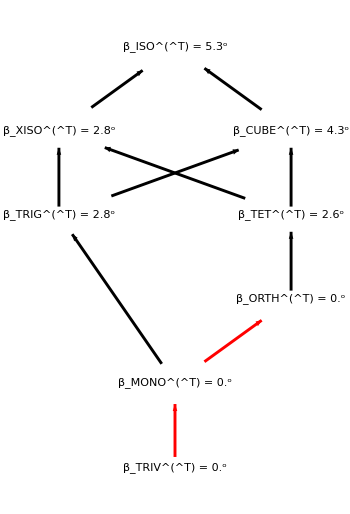

#### Igel, Mora, Riollet (1995) [units of 10^11 dyne/cm^2 = 10^10 N/m^2= 10 GPa; 1 dyne/cm^2 = 0.1 N/m^2] We multiply by 10 to put these in units of GPa.

```mathematica
CmatIgel=10({{10.0, 3.5, 2.5, -5.0, 0.1, 0.3}, {3.5, 8.0, 1.5, 0.2, -0.1, -0.15}, {2.5, 1.5, 6.0, 1.0, 0.4, 0.24}, {-5.0, 0.2, 1.0, 5.0, 0.35, 0.525}, {0.1, -0.1, 0.4, 0.35, 4.0, -1.0}, {0.3, -0.15, 0.24, 0.525, -1.0, 3.0}});
TmatIgel = TmatOfCmat[CmatIgel];
MatrixNote[TmatIgel]="T is Igel"
MatrixShortNote[TmatIgel]="Igel"
PrintVoigt[TmatIgel]
density[TmatIgel]=1000;
```

```mathematica
(*cmin=0;cmax=30; dc=3;
contoursMONO[TmatIgel]=Range[cmin,cmax,dc];
MaxForScaling[TmatIgel]=cmax-dc;*)
```

#### Map used in SSA2023 by Aakash Gupta, generated from ES_FarFromMono.nb This map is far from MONO, and its Poisson parameter for its closest ISO is near 0.25.

```mathematica
TmatSSA2023=({{0.317082, -0.00658517, 0.227862, 0.219176, 0.114762, -0.244823}, {-0.00658517, 0.07346, -0.114858, -0.0207015, 0.0275774, -0.142342}, {0.227862, -0.114858, 0.420424, 0.212793, 0.0528639, 0.120438}, {0.219176, -0.0207015, 0.212793, 0.241031, 0.102265, -0.162818}, {0.114762, 0.0275774, 0.0528639, 0.102265, 0.0962717, -0.147361}, {-0.244823, -0.142342, 0.120438, -0.162818, -0.147361, 0.64901}});
```

```mathematica
MatrixNote[TmatSSA2023]="T is SSA2023"
MatrixShortNote[TmatSSA2023]="SSA"
PrintVoigt[TmatSSA2023]
```

```mathematica
(*cmin=0;cmax=40; dc=4;
contoursMONO[TmatSSA2023]=Range[cmin,cmax,dc];
MaxForScaling[TmatSSA2023]=cmax-dc;*)
```

#### Rob Arts 1993 thesis, p. 243 Mensch and Rasolofosaon (1997 GJI), Appendix B Dry Vosges sandstone (Eq B4)

```mathematica
CmatArtsVosges=({{10.3, 0.9, 1.3, 1.4, 1.1, 0.8}, {0.9, 10.6, 2.1, 0.2, -0.2, -0.6}, {1.3, 2.1, 14.1, 0, -0.5, -1.0}, {1.4, 0.2, 0, 5.1, 0, 0.2}, {1.1, -0.2, -0.5, 0, 6.0, 0}, {0.8, -0.6, -1.0, 0.2, 0, 4.9}});
TmatArtsVosges = TmatOfCmat[CmatArtsVosges];
MatrixNote[TmatArtsVosges]="T is A-Vosges-sandstone"
MatrixShortNote[TmatArtsVosges]="AVos"
PrintVoigt[TmatArtsVosges]
density[TmatArtsVosges]=2080;
```

```mathematica
(*cmin=0;cmax=11; dc=1;
contoursMONO[TmatArtsVosges]=Range[cmin,cmax,dc];
MaxForScaling[TmatArtsVosges]=cmax-dc;*)
```

#### Vestrum et al. (1996), Table 2; also used in Dellinger (2005), Appendix A

```mathematica
CmatVestrum=({{16.85, 7.88, 6.81, 0.07, -0.18, 0.12}, {7.88, 16.03, 6.51, 0.00, -0.26, -0.08}, {6.81, 6.51, 11.14, 0.00, -0.05, -0.04}, {0.07, 0.00, 0.00, 3.03, 0.01, 0.04}, {-0.18, -0.26, -0.05, 0.01, 3.40, -0.01}, {0.12, -0.08, -0.04, 0.04, -0.01, 3.89}});
TmatVestrum = TmatOfCmat[CmatVestrum];
MatrixNote[TmatVestrum]="T is Vestrum"
MatrixShortNote[TmatVestrum]="Vest"
PrintVoigt[TmatVestrum]
density[TmatVestrum]=1300;  (* representative of "phenolic resin"; not listed in publication *)
```

```mathematica
(*cmin=0;cmax=8; dc=0.5;
contoursMONO[TmatVestrum]=Range[cmin,cmax,dc];
MaxForScaling[TmatVestrum]=cmax-dc;*)
```

#### Russell, Gaherty, et al. (2019 JGR), Table 1

```mathematica
CmatRussell2019=({{271.6149, 101.6837, 101.2700, 0, 0, −0.1902}, {101.6837, 233.9946, 99.9429, 0, 0, 0.3918}, {101.2700, 99.9429, 239.5542, 0, 0, 0.0071}, {0, 0, 0, 66.1769, 0.0452, 0}, {0, 0, 0, 0.0452, 74.6177, 0}, {−0.1902, 0.3918, 0.0071, 0, 0, 71.9655}});
TmatRussell2019 = TmatOfCmat[CmatRussell2019];
MatrixNote[TmatRussell2019]="T is Russell2019"
MatrixShortNote[TmatRussell2019]="Ru19"
PrintVoigt[TmatRussell2019]
```

#### density Russell (2024-07-29): “I double checked and the density used in the table in our 2019 paper was 3.35 g/cm^3.”

```mathematica
density[TmatRussell2022]=3350;
```

```mathematica
(*cmin=0;cmax=3.2; dc=0.4;
contoursMONO[TmatRussell2019]=Range[cmin,cmax,dc];
MaxForScaling[TmatRussell2019]=cmax-dc;*)
```

#### Russell, Gaherty, et al. (2022 JGR), Table 1

```mathematica
CmatRussell2022=({{243.5427, 71.5726, 73.6646, 0, 0, 1.5311}, {71.5726, 212.0492, 74.4322, 0, 0, 1.2569}, {73.6646, 74.4322, 213.2303, 0, 0, 0.0068}, {0, 0, 0, 68.5948, -0.0441, 0}, {0, 0, 0, -0.0441, 75.3675, 0}, {1.5311, 1.2569, 0.0068, 0, 0, 74.4751}});
TmatRussell2022 = TmatOfCmat[CmatRussell2022];
MatrixNote[TmatRussell2022]="T is Russell2022"
MatrixShortNote[TmatRussell2022]="Ru22"
PrintVoigt[TmatRussell2022]
```

#### density 3300 matches the velocity values shown in Figure 2c (confirmed by Russell 2024-07-31) Russell (2024-07-31): use 3342, which is the average over the upper ~7 km of the model (see Table S1) Russell (2024-07-31) sent an updated pole figure based on the density of 3342.

```mathematica
density[TmatRussell2022]=3342;
```

#### Francois, Geymonat, Berthaud (1998), Table 3 superalloy monocrystal (NOT oak) And also Norris (2006), Eq. 74 [who note a typo in the original for the C53 entry [the corrected entry was confirmed by C. Tape e-communication with Francois in July 2024, whereby Francois’ Matlab code lists the correct values] see Check_Tmat_FrancoisNorris.nb

```mathematica
CmatFrancois=1.({{243, 136, 135, 22, 52, -17}, {136, 239, 137, -28, 11, 16}, {135, 137, 233, 29, -49, 3}, {22, -28, 29, 133, -10, -4}, {52, 11, -49, -10, 119, -2}, {-17, 16, 3, -4, -2, 130}});
TmatFrancois = TmatOfCmat[CmatFrancois];
MatrixNote[TmatFrancois]="T is Francois"
MatrixShortNote[TmatFrancois]="Fra"
PrintVoigt[TmatFrancois]
```

#### density The value was obtained via e-communication from M. Francois on 2023-07-03; it not listed in the 1998 publication or the 1995 thesis.

```mathematica
density[TmatFrancois]=8600;
```

```mathematica
(*cmin=0;cmax=20; dc=2;
contoursMONO[TmatFrancois]=Range[cmin,cmax,dc];
MaxForScaling[TmatFrancois]=cmax-dc;*)
```

#### Francois (1995) thesis, p. 53: oak wood

```mathematica
CmatFrancoisOak=({{3.51, 0.47, 1.27, -0.56, -0.67, -0.02}, {0.47, 13.20, 1.03, 0.24, -0.04, -0.07}, {1.27, 1.03, 2.97, 0.14, -0.23, -0.59}, {-0.56, 0.24, 0.14, 0.37, 0.17, 0.06}, {-0.67, -0.04, -0.23, 0.17, 1.09, -0.07}, {-0.02, -0.07, -0.59, 0.06, -0.07, 0.81}});
TmatFrancoisOak = TmatOfCmat[CmatFrancoisOak];
MatrixNote[TmatFrancoisOak]="T is FrancoisOak"
MatrixShortNote[TmatFrancoisOak]="Foak"
PrintVoigt[TmatFrancoisOak]
density[TmatFrancoisOak]=953;
```

#### Francois (1995) thesis, p. 53: beech wood THIS ELASTIC MAP HAS A NEGATIVE EIGENVALUE.

```mathematica
CmatFrancoisBeech=({{2.45, 4.58, 0.91, -0.59, 0.27, 0.13}, {4.58, 19.47, 0.80, 1.64, -1.02, -0.77}, {0.91, 0.80, 4.70, 0.70, 0.25, -0.88}, {-0.59, 1.64, 0.70, 3.15, 0.32, -0.17}, {0.27, -1.02, 0.25, 0.32, 1.08, -0.86}, {0.13, -0.77, -0.88, -0.17, -0.86, 2.54}});
TmatFrancoisBeech = TmatOfCmat[CmatFrancoisBeech];
MatrixNote[TmatFrancoisBeech]="T is FrancoisBeech"
MatrixShortNote[TmatFrancoisBeech]="Fbch"
PrintVoigt[TmatFrancoisBeech]
density[TmatFrancoisBeech]=897.6;
```

#### Francois (1995) thesis, p. 53: beech wood PERTURBED SUCH THAT IT HAS POSITIVE EIGENVALUES

```mathematica
tpert=tpertTmat[TmatFrancoisBeech,0.01,0.1,-2]+0.01
TmatFrancoisBeechPert = Tpert[TmatFrancoisBeech,tpert];
MatrixNote[TmatFrancoisBeechPert]="T is FrancoisBeechPert"
MatrixShortNote[TmatFrancoisBeechPert]="Fbchp"
PrintVoigt[TmatFrancoisBeechPert]
density[TmatFrancoisBeechPert]=density[TmatFrancoisBeech];
```

#### Francois (1995) thesis, p. 53: sipo mahogany wood THIS ELASTIC MAP HAS A NEGATIVE EIGENVALUE.

```mathematica
CmatFrancoisSipo=({{2.31, 0.26, 0.18, 0.28, 0.09, -0.25}, {0.26, 1.54, 1.23, 0.19, 1.02, 0.05}, {0.18, 1.23, 12.32, 1.63, 0.15, 0.01}, {0.28, 0.19, 1.63, 0.53, 0.51, -0.02}, {0.09, 1.02, 0.15, 0.51, 0.38, -0.11}, {-0.25, 0.05, 0.01, -0.02, -0.11, 0.61}});
TmatFrancoisSipo = TmatOfCmat[CmatFrancoisSipo];
MatrixNote[TmatFrancoisSipo]="T is FrancoisSipo"
MatrixShortNote[TmatFrancoisSipo]="Fspo"
PrintVoigt[TmatFrancoisSipo]
density[TmatFrancoisSipo]=585;
```

#### Francois (1995) thesis, p. 53: sipo mahogany wood PERTURBED SUCH THAT IT HAS POSITIVE EIGENVALUES

```mathematica
tpert=tpertTmat[TmatFrancoisSipo,0.01,0.3,-2]+0.01
TmatFrancoisSipoPert = Tpert[TmatFrancoisSipo,tpert];
MatrixNote[TmatFrancoisSipoPert]="T is FrancoisSipoPert"
MatrixShortNote[TmatFrancoisSipoPert]="Fspop"
PrintVoigt[TmatFrancoisSipoPert]
density[TmatFrancoisSipoPert]=density[TmatFrancoisSipo];
```

#### Francois (1995) thesis, p. 54: dry Vosges sandstone

```mathematica
CmatFrancoisVosges=({{12.2, -2.2, 1.9, 0.9, 0.8, -0.5}, {-2.2, 13.0, 2.9, 0.2, -0.3, 0.4}, {1.9, 2.9, 13.9, 0.0, -0.0, 0.1}, {0.9, 0.2, 0.0, 4.0, 1.2, 0.0}, {0.8, -0.3, -0.0, 1.2, 5.4, 0.0}, {-0.5, 0.4, 0.1, 0.0, 0.0, 5.4}});
TmatFrancoisVosges = TmatOfCmat[CmatFrancoisVosges];
MatrixNote[TmatFrancoisVosges]="T is F-Vosges-sandstone"
MatrixShortNote[TmatFrancoisVosges]="FVos"
PrintVoigt[TmatFrancoisVosges]
density[TmatFrancoisVosges]=density[TmatArtsVosges];
```

```mathematica
(*cmin=0;cmax=11; dc=1;
contoursMONO[TmatArtsVosges]=Range[cmin,cmax,dc];
MaxForScaling[TmatArtsVosges]=cmax-dc;*)
```

#### Ashman, Cowin, Van Buskirk, Rice (1984), Table 4. See also Cowin and Mehrabadi (1989), who rotate this map as part of a numerical example. This orthorhombic map is based on measurements averaged from 60 human bone specimens. “Average elastic coefficients measured from fresh unembalmed human and canine femora”

```mathematica
CmatAshmanHuman=({{18.0, 9.98, 10.1, 0, 0, 0}, {9.98, 20.2, 10.7, 0, 0, 0}, {10.1, 10.7, 27.6, 0, 0, 0}, {0, 0, 0, 6.23, 0, 0}, {0, 0, 0, 0, 5.61, 0}, {0, 0, 0, 0, 0, 4.52}});
TmatAshmanHuman = TmatOfCmat[CmatAshmanHuman];
MatrixNote[TmatAshmanHuman]="T is Ashman1984human"
MatrixShortNote[TmatAshmanHuman]="A84h"
PrintVoigt[TmatAshmanHuman]
density[TmatAshmanHuman]=1900;   (* inferred from Figure 9 *)
```

#### Ashman, Cowin, Van Buskirk, Rice (1984), Table 4. See also Cowin and Mehrabadi (1989). This orthorhombic map is based on measurements averaged from 120 canine bone specimens. “Average elastic coefficients measured from fresh unembalmed human and canine femora”

```mathematica
CmatAshmanCanine=({{19.0, 9.73, 11.9, 0, 0, 0}, {9.73, 22.2, 11.9, 0, 0, 0}, {11.9, 11.9, 29.7, 0, 0, 0}, {0, 0, 0, 6.67, 0, 0}, {0, 0, 0, 0, 5.67, 0}, {0, 0, 0, 0, 0, 4.67}});
TmatAshmanCanine = TmatOfCmat[CmatAshmanCanine];
MatrixNote[TmatAshmanCanine]="T is Ashman1984canine"
MatrixShortNote[TmatAshmanCanine]="A84c"
PrintVoigt[TmatAshmanCanine]
density[TmatAshmanCanine]=1875;   (* inferred from Figure 9 *)
```

#### Lokajicek et al. (2021), Table 3, WG100, 0.1 MPa

```mathematica
CmatLokajicekWG100lp=({{47.6, 16.7, 16.3, 0.1, -1.1, -2}, {16.7, 51.1, 16.8, 0, -0.6, -2.1}, {16.3, 16.8, 51.7, 0.2, -1.8, -1.2}, {0.1, 0, 0.2, 16.8, -0.2, -0.2}, {-1.1, -0.6, -1.8, -0.2, 16.8, 0.1}, {-2, -2.1, -1.2, -0.2, 0.1, 16.8}});
```

```mathematica
TmatLokajicekWG100lp = TmatOfCmat[CmatLokajicekWG100lp];
MatrixNote[TmatLokajicekWG100lp]="T is Lokajicek-WG100-lp"
MatrixShortNote[TmatLokajicekWG100lp]="Lok1"
PrintVoigt[TmatLokajicekWG100lp]
density[TmatLokajicekWG100lp]=2635;
```

```mathematica
(*cmin=0;cmax=4.5; dc=0.5;
contoursMONO[TmatLokajicekWG100lp]=Range[cmin,cmax,dc];
MaxForScaling[TmatLokajicekWG100lp]=cmax-dc;*)
```

#### Lokajicek et al. (2021), Table 3, WG100, 400 MPa

```mathematica
CmatLokajicekWG100hp=({{101.4, 34.8, 34.4, 0.2, 0.6, 0.7}, {34.8, 100.8, 33.4, 0.9, 0.9, 1}, {34.4, 33.4, 104.4, 0.9, 0.4, 0.4}, {0.2, 0.9, 0.9, 34.1, 0.1, 0.2}, {0.6, 0.9, 0.4, 0.1, 34.3, 0}, {0.7, 1, 0.4, 0.2, 0, 34.4}});
```

```mathematica
TmatLokajicekWG100hp = TmatOfCmat[CmatLokajicekWG100hp];
MatrixNote[TmatLokajicekWG100hp]="T is Lokajicek-WG100-hp"
MatrixShortNote[TmatLokajicekWG100hp]="Lok2"
PrintVoigt[TmatLokajicekWG100hp]
density[TmatLokajicekWG100hp]=density[TmatLokajicekWG100lp];
```

```mathematica
(*cmin=0;cmax=1.3; dc=0.1;
contoursMONO[TmatLokajicekWG100hp]=Range[cmin,cmax,dc];
MaxForScaling[TmatLokajicekWG100hp]=cmax-dc;*)
```

#### Lokajicek et al. (2021), Table 3, WG600, 0.1 MPa

```mathematica
CmatLokajicekWG600lp=({{3.5, 1.3, 1.3, 0, -0.2, -0.5}, {1.3, 3.4, 1.2, -0.1, -0.1, -0.4}, {1.3, 1.2, 3.4, -0.1, -0.2, -0.2}, {0, -0.1, -0.1, 1.2, 0, 0}, {-0.2, -0.1, -0.2, 0, 1.2, 0}, {-0.5, -0.4, -0.2, 0, 0, 1.3}});
```

```mathematica
TmatLokajicekWG600lp = TmatOfCmat[CmatLokajicekWG600lp];
MatrixNote[TmatLokajicekWG600lp]="T is Lokajicek-WG600-lp"
MatrixShortNote[TmatLokajicekWG600lp]="Lok3"
PrintVoigt[TmatLokajicekWG600lp]
density[TmatLokajicekWG600lp]=density[TmatLokajicekWG100lp];
```

```mathematica
(*cmin=0;cmax=11; dc=1;
contoursMONO[TmatLokajicekWG600lp]=Range[cmin,cmax,dc];
MaxForScaling[TmatLokajicekWG600lp]=cmax-dc;*)
```

#### Lokajicek et al. (2021), Table 3, WG600, 400 MPa

```mathematica
CmatLokajicekWG600hp=({{99.5, 32.8, 33.0, 0.7, -0.2, 0.8}, {32.8, 99.3, 33.2, 1.0, 0.5, 1.0}, {33.0, 33.2, 102.3, 0.6, 0, 0.7}, {0.7, 1.0, 0.6, 33.5, 0.1, 0.1}, {-0.2, 0.5, 0, 0.1, 33.5, 0.1}, {0.8, 1.0, 0.7, 0.1, 0.1, 33.4}});
```

```mathematica
TmatLokajicekWG600hp = TmatOfCmat[CmatLokajicekWG600hp];
MatrixNote[TmatLokajicekWG600hp]="T is Lokajicek-WG600-hp"
MatrixShortNote[TmatLokajicekWG600hp]="Lok4"
PrintVoigt[TmatLokajicekWG600hp]
density[TmatLokajicekWG600hp]=density[TmatLokajicekWG100lp];
```

```mathematica
(*cmin=0;cmax=1.3; dc=0.1;
contoursMONO[TmatLokajicekWG600hp]=Range[cmin,cmax,dc];
MaxForScaling[TmatLokajicekWG600hp]=cmax-dc;*)
```

#### THIS IS A MAP FOR TESTING ONLY Becker et al. (2008, 2014) https://www-udc.ig.utexas.edu/external/becker/anisotropy_model.html Line 12794 of safs417nc3_er.s.0.75.WLD.200.savd.dat

```mathematica
CmatBecker=({{2.51779*^2, 9.32360*^1, 8.44840*^1, 7.62656*^-1, 1.08919, 1.28893*^1}, {9.32360*^1, 2.33514*^2, 8.64265*^1, 1.21066, 6.10859*^-1, 7.16282}, {8.44840*^1, 8.64265*^1, 2.14772*^2, 5.12094*^-1, 1.80794*^-1, -1.88478}, {7.62656*^-1, 1.21066, 5.12094*^-1, 6.82019*^1, 3.21513, 8.08571*^-1}, {1.08919, 6.10859*^-1, 1.80794*^-1, 3.21513, 7.07792*^1, 8.87808*^-1}, {1.28893*^1, 7.16282, -1.88478, 8.08571*^-1, 8.87808*^-1, 7.90952*^1}});
```

```mathematica
TmatBecker = TmatOfCmat[CmatBecker];
MatrixNote[TmatBecker]="T is Becker"
MatrixShortNote[TmatBecker]="Becker"
PrintVoigt[TmatBecker]
```

```mathematica
(*cmin=0;cmax=5; dc=0.5;
contoursMONO[TmatBecker]=Range[cmin,cmax,dc];
MaxForScaling[TmatBecker]=cmax-dc;*)
```

```mathematica
(* MinimizationFacts[TmatBecker,XISO]*)
```

#### Schulte-Pelkum and Blackman (2002), Table 1, Triclinic

```mathematica
CmatSPB2002triclinic=({{260.9, 68.4, 65.2, 2.0, -0.4, -1.3}, {68.4, 228.7, 72.0, 0.9, 1.1, -0.7}, {65.2, 72.0, 207.8, -1.1, -0.3, -1.0}, {2.0, 0.9, -1.1, 72.2, -1.5, 0.1}, {-0.4, 1.1, -0.3, -1.5, 75.6, 1.3}, {-1.3, -0.7, -1.0, 0.1, 1.3, 83.5}});
```

```mathematica
TmatSPB2002triclinic = TmatOfCmat[CmatSPB2002triclinic];
MatrixNote[TmatSPB2002triclinic]="T is SPB-triclinic"
MatrixShortNote[TmatSPB2002triclinic]="SPBt"
PrintVoigt[TmatSPB2002triclinic]
density[TmatSPB2002triclinic]=3353;
```

## Ismail and Mainprice (1998) maps (Table 2)

#### Total database

```mathematica
CmatIsmailMainpriceTotal=({{195.45, 71.11, 72.08, -0.06, -0.09, -0.08}, {71.11, 236.91, 72.37, 0.17, -0.20, -0.11}, {72.08, 72.37, 205.92, 0.37, -0.21, -00.09}, {-0.06, 0.17, 0.37, 71.37, -0.18, -0.36}, {-0.09, -0.20, -0.21, -0.18, 62.99, 0.06}, {-0.08, -0.11, -0.09, -0.36, 0.06, 69.77}});
```

```mathematica
TmatIsmailMainpriceTotal = TmatOfCmat[CmatIsmailMainpriceTotal];
MatrixNote[TmatIsmailMainpriceTotal]="T is IM1998-total"
MatrixShortNote[TmatIsmailMainpriceTotal]="IMtot"
PrintVoigt[TmatIsmailMainpriceTotal]
```

```mathematica
(*cmin=0;cmax=4; dc=0.4;
contoursMONO[TmatIsmailMainpriceTotal]=Range[cmin,cmax,dc];
MaxForScaling[TmatIsmailMainpriceTotal]=cmax-dc;*)
```

#### Fast spreading ridge

```mathematica
CmatIsmailMainpriceRidge=({{195.91, 71.12, 72.21, -0.07, -0.24, -0.14}, {71.12, 239.36, 71.87, 0.03, -0.36, -0.16}, {72.21, 71.87, 203.72, 0.40, -0.39, 0.02}, {-0.07, 0.03, 0.40, 71.05, -0.15, -0.60}, {-0.24, -0.36, -0.39, -0.15, 62.49, 0.01}, {-0.14, -0.16, 0.02, -0.60, 0.01, 70.24}});
```

```mathematica
TmatIsmailMainpriceRidge = TmatOfCmat[CmatIsmailMainpriceRidge];
MatrixNote[TmatIsmailMainpriceRidge]="T is IM1998-spreading-ridge"
MatrixShortNote[TmatIsmailMainpriceRidge]="IMrdg"
PrintVoigt[TmatIsmailMainpriceRidge]
```

```mathematica
(*cmin=0;cmax=4.4; dc=0.4;
contoursMONO[TmatIsmailMainpriceRidge]=Range[cmin,cmax,dc];
MaxForScaling[TmatIsmailMainpriceRidge]=cmax-dc;*)
```

#### Subduction zone

```mathematica
CmatIsmailMainpriceSubduction=({{192.07, 69.92, 72.35, 0.21, -0.04, 0.10}, {69.92, 237.08, 73.47, -0.31, 0.25, 0.61}, {72.35, 73.47, 208.75, -0.30, 0.23, -0.28}, {0.21, -0.31, -0.30, 72.55, 0.01, 0.38}, {-0.04, 0.25, 0.23, 0.01, 63.28, 0.09}, {0.10, 0.61, -0.28, 0.38, 0.09, 68.5}});
```

```mathematica
TmatIsmailMainpriceSubduction = TmatOfCmat[CmatIsmailMainpriceSubduction];
MatrixNote[TmatIsmailMainpriceSubduction]="T is IM1998-subduction"
MatrixShortNote[TmatIsmailMainpriceSubduction]="IMsub"
PrintVoigt[TmatIsmailMainpriceSubduction]
```

```mathematica
(*cmin=0;cmax=4.4; dc=0.4;
contoursMONO[TmatIsmailMainpriceSubduction]=Range[cmin,cmax,dc];
MaxForScaling[TmatIsmailMainpriceSubduction]=cmax-dc;*)
```

#### Kimberlites

```mathematica
CmatIsmailMainpriceKimberlite=({{194.51, 70.79, 71.83, -0.12, 0.78, -0.36}, {70.79, 229.24, 73.21, 0.32, 0.19, 0.01}, {71.83, 73.21, 213.98, -0.22, 0.52, -0.22}, {-0.12, 0.32, -0.22, 71.66, -0.06, 0.38}, {0.78, 0.19, 0.52, -0.06, 64.49, -0.13}, {-0.36, 0.01, -0.22, 0.38, -0.13, 68.27}});
```

```mathematica
TmatIsmailMainpriceKimberlite = TmatOfCmat[CmatIsmailMainpriceKimberlite];
MatrixNote[TmatIsmailMainpriceKimberlite]="T is IM1998-kimberlite"
MatrixShortNote[TmatIsmailMainpriceKimberlite]="IMkim"
PrintVoigt[TmatIsmailMainpriceKimberlite]
```

```mathematica
(*cmin=0;cmax=3.6; dc=0.4;
contoursMONO[TmatIsmailMainpriceKimberlite]=Range[cmin,cmax,dc];
MaxForScaling[TmatIsmailMainpriceKimberlite]=cmax-dc;*)
```

## Ji, Zhao, Francis (1994) maps (Table 1)

#### Castle Rock

```mathematica
CmatJi1994CastleRock=({{228.05, 66.26, 68.07, -0.12, -0.12, -0.94}, {66.26, 195.91, 68.25, -0.08, 0.11, -0.18}, {68.07, 68.25, 201.65, -0.37, 0.02, 0.36}, {-0.12, -0.08, -0.37, 65.00, 0.07, 0.12}, {-0.12, 0.11, 0.02, 0.07, 71.06, -0.41}, {-0.94, -0.18, 0.36, 0.12, -0.41, 69.61}});
```

```mathematica
TmatJi1994CastleRock = TmatOfCmat[CmatJi1994CastleRock];
MatrixNote[TmatJi1994CastleRock]="T is Ji1994-CastleRock"
MatrixShortNote[TmatJi1994CastleRock]="JiCR"
PrintVoigt[TmatJi1994CastleRock]
```

```mathematica
(*cmin=0;cmax=3.2; dc=0.4;
contoursMONO[TmatJi1994CastleRock]=Range[cmin,cmax,dc];
MaxForScaling[TmatJi1994CastleRock]=cmax-dc;*)
```

#### Alligator Lake

```mathematica
CmatJi1994AlligatorLake=({{214.57, 67.34, 68.54, -0.09, 0.38, 0.40}, {67.34, 200.38, 68.01, 0.50, 0.26, 0.94}, {68.54, 68.01, 211.04, -0.43, 0.49, 0.02}, {-0.09, 0.50, -0.43, 67.79, 0.56, 0.20}, {0.38, 0.26, 0.49, 0.56, 71.24, 0.01}, {0.40, 0.94, 0.02, 0.20, 0.01, 69.51}});
```

```mathematica
TmatJi1994AlligatorLake = TmatOfCmat[CmatJi1994AlligatorLake];
MatrixNote[TmatJi1994AlligatorLake]="T is Ji1994-AlligatorLake"
MatrixShortNote[TmatJi1994AlligatorLake]="JiAL"
PrintVoigt[TmatJi1994AlligatorLake]
```

```mathematica
(*cmin=0;cmax=1.6; dc=0.2;
contoursMONO[TmatJi1994AlligatorLake]=Range[cmin,cmax,dc];
MaxForScaling[TmatJi1994AlligatorLake]=cmax-dc;*)
```

#### Nunivak Island

```mathematica
CmatJi1994NunivakIsland=({{224.44, 67.27, 70.71, -0.28, -0.33, -0.94}, {67.27, 193.13, 68.69, 0.29, 0.19, -0.88}, {70.71, 68.69, 210.52, 0.57, -0.25, -0.25}, {-0.28, 0.29, 0.57, 65.52, -0.65, 0.00}, {-0.33, 0.19, -0.25, -0.65, 73.03, -0.05}, {-0.94, -0.88, -0.25, 0.00, -0.05, 68.65}});
```

```mathematica
TmatJi1994NunivakIsland = TmatOfCmat[CmatJi1994NunivakIsland];
MatrixNote[TmatJi1994NunivakIsland]="T is Ji1994-NunivakIsland"
MatrixShortNote[TmatJi1994NunivakIsland]="JiNI"
PrintVoigt[TmatJi1994NunivakIsland]
```

```mathematica
(*cmin=0;cmax=3.2; dc=0.4;
contoursMONO[TmatJi1994NunivakIsland]=Range[cmin,cmax,dc];
MaxForScaling[TmatJi1994NunivakIsland]=cmax-dc;*)
```

## Maps from Tape and Tape (2024) – TmatMar17

#### TmatMar17 - exact expression

```mathematica
TmatPert=({{474, 22, 22, 18, 4, 10}, {22, 374, -22, 28, -16, -34}, {22, -22, 318, 6, -26, 6}, {18, 28, 6, 262, 8, 14}, {4, -16, -26, 8, 32, 42}, {10, -34, 6, 14, 42, 74}});
```

```mathematica
Urot=ZRot[-20.Degree].XRot[-30Degree];
TmatMar17exact=MatrixUbar[Urot].TmatPert.Transpose[MatrixUbar[Urot]];
MatrixNote[TmatMar17exact]="T is Mar17x"
MatrixShortNote[TmatMar17exact]="Mar17x"
PrintVoigt[TmatMar17exact]
```

#### TmatMar17 (Eq. 93) - rounded to 0.1 This is the version used in the paper.

```mathematica
TmatMar17=({{206.2, -67.4, 17.1, -15.9, 166.6, -19.5}, {-67.4, 352.9, 32.2, 3.3, 61.6, -41.6}, {17.1, 32.2, 343.8, 0.4, 73.6, -4.2}, {-15.9, 3.3, 0.4, 270.0, 88.8, 13.3}, {166.6, 61.6, 73.6, 88.8, 287.1, 30.7}, {-19.5, -41.6, -4.2, 13.3, 30.7, 74.0}});
```

```mathematica
MatrixNote[TmatMar17]="T is Mar17"
MatrixShortNote[TmatMar17]="Mar17"
PrintVoigt[TmatMar17]
```

```mathematica
(*cmin=0;cmax=27; dc=3;
contoursMONO[TmatMar17]=Range[cmin,cmax,dc];
MaxForScaling[TmatMar17]=cmax-dc;*)
```

#### Rounded versions used in MSAT

```mathematica
Print["The Voigt matrix is ",DispMat[Simplify[CmatOfTmat[TmatMar17exact]],1]];
```

```mathematica
Print["The Voigt matrix is ",DispMat[Simplify[CmatOfTmat[TmatMar17]],1]];
```

#### U obtained from MSAT (use for node mode 1)

```mathematica
RfromMSATMar17=({{0.468078008543277, 0.261329948254664, 0.844162091107729}, {0.804629451471810, -0.520976355566523, -0.284877311776136}, {0.365341516587334, 0.812582485096645, -0.454131347929019}}); 
UfromMSATMar17 =Transpose[RfromMSATMar17];
```

```mathematica
RfromMSATMar17STIFF=({{-0.427114116100300, -0.789118875485163, 0.441435082634912}, {-0.745745521753299, 0.583505623551795, 0.321535074398317}, {-0.511309249488760, -0.191866066922902, -0.837705356166938}});
UfromMSATMar17STIFF =Transpose[RfromMSATMar17STIFF];
```

```mathematica
RfromMSATMar17STIFFwithCrounded=({{-0.4284, -0.7880, 0.4422}, {-0.7448, 0.5850, 0.3210}, {-0.5116, -0.1919, -0.8375}});
```

```mathematica
UfromMSATMar17STIFFwithCrounded=Transpose[RfromMSATMar17STIFFwithCrounded];
UfromMSATMar17STIFFwithCroundedmod=UfromMSATMar17STIFFwithCrounded.YRot[π].ZRot[-40Degree];
```

#### TmatMar17 - modified to have a more physical Poisson parameter (for closest ISO) The difference is that the (6,6) entry is 656 larger than the (6,6) entry of TmatMar17.

```mathematica
TISO=Closest[TmatMar17,ISO];
Tdiff=TmatMar17-TISO;
TISOmod=TISO; TISOmod[[6,6]]=730;
TmatMar17mod=Tdiff+TISOmod;
```

```mathematica
MatrixNote[TmatMar17mod]="T is Mar17mod"
MatrixShortNote[TmatMar17mod]="Mar17mod"
PrintVoigt[TmatMar17mod]
```

```mathematica
(*cmin=0;cmax=20; dc=2;
contoursMONO[TmatMar17mod]=Range[cmin,cmax,dc];
MaxForScaling[TmatMar17mod]=cmax-dc;*)
```

#### differences in T and in C

```mathematica
MatrixForm[TmatMar17mod-TmatMar17]
MatrixForm[CmatOfTmat[TmatMar17mod]]
MatrixForm[CmatOfTmat[TmatMar17mod]-CmatOfTmat[TmatMar17]]
```

#### U obtained from MSAT (use for node mode 1)

```mathematica
RfromMSATMar17mod=({{-0.468078008543277, -0.261329948254664, -0.844162091107729}, {-0.804629451471809, 0.520976355566525, 0.284877311776135}, {0.365341516587337, 0.812582485096643, -0.454131347929020}}); 
UfromMSATMar17mod =Transpose[RfromMSATMar17mod];
```

## Maps from Tape and Tape (2024)

#### MONO map a (Eq. 57) - TmatJuly16

```mathematica
TT24MONOa=({{1, 0, 0, 0, 0, 0}, {0, 2, 0, 0, 0, 0}, {0, 0, 3, 2, 1, 0}, {0, 0, 2, 4, 0, 0}, {0, 0, 1, 0, 5, 0}, {0, 0, 0, 0, 0, 6}});
```

```mathematica
MatrixNote[TT24MONOa]="T is TT24MONOa"
MatrixShortNote[TT24MONOa]="MONOa"
PrintVoigt[TT24MONOa]
```

```mathematica
Print["The Voigt matrix is ",MatrixForm[Simplify[1.CmatOfTmat[TT24MONOa]]]];
```

#### MONO map b (Eq. 59) - TmatJune8

```mathematica
TT24MONOb=({{28, -2, 0, 0, 0, 0}, {-2, 61, 0, 0, 0, 0}, {0, 0, 71, -4, 6, 8}, {0, 0, -4, 68, 10, 0}, {0, 0, 6, 10, 62, -3}, {0, 0, 8, 0, -3, 59}});
```

```mathematica
MatrixNote[TT24MONOb]="T is TT24MONOb"
MatrixShortNote[TT24MONOb]="MONOb"
PrintVoigt[TT24MONOb]
```

```mathematica
Print["The Voigt matrix is ",MatrixForm[Simplify[1.CmatOfTmat[TT24MONOb]]]];
```

#### ORTH map a (Eq. 62) - TmatJune12

```mathematica
TT24ORTHa=({{86, 0, 0, 0, 0, 0}, {0, 51, 0, 0, 0, 0}, {0, 0, 32, 0, 0, 0}, {0, 0, 0, 46, -20, 13}, {0, 0, 0, -20, 45, -2}, {0, 0, 0, 13, -2, 87}});
```

```mathematica
MatrixNote[TT24ORTHa]="T is TT24ORTHa"
MatrixShortNote[TT24ORTHa]="ORTHa"
PrintVoigt[TT24ORTHa]
```

```mathematica
Print["The Voigt matrix is ",MatrixForm[Simplify[1.CmatOfTmat[TT24ORTHa]]]]
```

#### ORTH map b (Eq. 77a) - ORTHtest (BC_BrowaeysChevrotNotes.nb)

```mathematica
TT24ORTHb=({{1, 0, 0, 0, 0, 0}, {0, 2, 0, 0, 0, 0}, {0, 0, 5, 0, 0, 0}, {0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 1}});
```

```mathematica
MatrixNote[TT24ORTHb]="T is TT24ORTHb"
MatrixShortNote[TT24ORTHb]="ORTHb"
PrintVoigt[TT24ORTHb]
```

#### TET map a (Eq. 65) - TmatJuly22TET

```mathematica
TT24TETa=({{60, 0, 0, 0, 0, 0}, {0, 60, 0, 0, 0, 0}, {0, 0, 15, 0, 0, 0}, {0, 0, 0, 71, 0, 0}, {0, 0, 0, 0, 58, 6}, {0, 0, 0, 0, 6, 15}});
```

```mathematica
MatrixNote[TT24TETa]="T is TT24TETa"
MatrixShortNote[TT24TETa]="TETa"
PrintVoigt[TT24TETa]
```

```mathematica
Print["The Voigt matrix is ",MatrixForm[Simplify[1.CmatOfTmat[TT24TETa]]]]
```

#### TET map b (Eq. 67) - TmatSep6TET

```mathematica
TT24TETb=({{2, 0, 0, 0, 0, 0}, {0, 2, 0, 0, 0, 0}, {0, 0, 3, 0, 0, 0}, {0, 0, 0, 1, 0, 0}, {0, 0, 0, 0, 2, 0}, {0, 0, 0, 0, 0, 1}});
```

```mathematica
MatrixNote[TT24TETb]="T is TT24TETb"
MatrixShortNote[TT24TETb]="TETb"
PrintVoigt[TT24TETb]
```

```mathematica
Print["The Voigt matrix is ",MatrixForm[Simplify[1.CmatOfTmat[TT24TETb]]]]
```

#### XISO maps in Figure 6 (see BC_TsubXISO_2024-01-26.nb)

#### two reference matrices

```mathematica
Tmat1=TmatForXISO/.{a->1.,c->2.,e->3.,f->4.,k->0};
Tmat2=TmatForXISO/.{a->1.,c->1.5,e->2.3,f->3.5,k->0};
MatrixForm[Tmat1]
MatrixForm[Tmat2]
```

#### two U

```mathematica
θ1=-60.Degree;
ϕ1=30.Degree;
U1=UsHat[{θ1,0,ϕ1}];
θ2=40.Degree;
ϕ2=40.Degree;
U2=UsHat[{θ2,0,ϕ2}];
DispMat[U1,3]
DispMat[U2,3]
```

#### four maps (from left to right in Figure 6)

```mathematica
TT24XISOa=Conj[Tmat2,U1];
TT24XISOb=Conj[Tmat1,U1];
TT24XISOc=Conj[Tmat1,U2];
TT24XISOd=Conj[Tmat2,U2];
```

```mathematica
(*optionsX ={ViewPoint->20xyztp[{0,70}],Lighting->{{"Ambient",White}},Boxed->False};
contoursX=contours[TT24XISOc,MONO]
MaxForScalingX=MaxForScaling[TT24XISOc,MONO]
MaxForScalingX=contoursX[[-1]]
Show[cpMONO[TT24XISOa,contoursX,MaxForScalingX,plotpoints,contourstyle],{optionsX}]
Show[cpMONO[TT24XISOb,contoursX,MaxForScalingX,plotpoints,contourstyle],{optionsX}]
Show[cpMONO[TT24XISOc,contoursX,MaxForScalingX,plotpoints,contourstyle],{optionsX}]
Show[cpMONO[TT24XISOd,contoursX,MaxForScalingX,plotpoints,contourstyle],{optionsX}]*)
```

```mathematica
PrintVoigt[TT24XISOa]
```

```mathematica
PrintVoigt[TT24XISOb]
```

```mathematica
PrintVoigt[TT24XISOc]
```

```mathematica
PrintVoigt[TT24XISOd]
```

## Maps from Tape and Tape (2022) – see ES_RefMatricesForCollage.nb

## Maps from Tape and Tape (2021)

#### TRIV (Eq. 23)

```mathematica
TT21TRIVnodenom=({{5, 0, 0, -2, 0, 0}, {0, 6, 0, 0, -2, 0}, {0, 0, 5, 0, 0, 0}, {-2, 0, 0, 5, 0, 0}, {0, -2, 0, 0, 6, 0}, {0, 0, 0, 0, 0, 6}});
```

```mathematica
denominator=5;
TT21TRIV=1/denominator TT21TRIVnodenom;
```

```mathematica
MatrixNote[TT21TRIV]="T is TT21TRIV"
MatrixShortNote[TT21TRIV]="TRIV"
PrintVoigt[TT21TRIV]
```

#### MONO (Section 15.1)

```mathematica
denominator=80;
TT21MONO=1/denominator({{222, -12 √6, -82, 21 √6, -39 √2, 0}, {-12 √6, 196, 12 √6, 30, 10 √3, -16}, {-82, 12 √6, 222, 9 √6, -51 √2, 0}, {21 √6, 30, 9 √6, 242, -6 √3, -24}, {-39 √2, 10 √3, -51 √2, -6 √3, 254, -8 √3}, {0, -16, 0, -24, -8 √3, 304}});
```

```mathematica
MatrixNote[TT21MONO]="T is TT21MONO"
MatrixShortNote[TT21MONO]="MONO"
PrintVoigt[TT21MONO]
MatrixForm[N[TT21MONO]]
```

#### ORTH (Section 15.2)

```mathematica
denominator=10;
TT21ORTH=1/denominator({{38, 18, 3 √2, -5 √2, -√6, -√8}, {18, 38, 3 √2, 5 √2, -√6, -√8}, {3 √2, 3 √2, 41, 0, -7 √3, 6}, {-5 √2, 5 √2, 0, 20, 0, 0}, {-√6, -√6, -7 √3, 0, 27, -2 √3}, {-√8, -√8, 6, 0, -2 √3, 56}});
```

```mathematica
MatrixNote[TT21ORTH]="T is TT21ORTH"
MatrixShortNote[TT21ORTH]="ORTH"
PrintVoigt[TT21ORTH]
MatrixForm[N[TT21ORTH]]
```

#### TET (Section 15.3)

```mathematica
denominator=64;
TT21TET=1/denominator({{168, 4 √6, -40, 6 √6, 6 √2, 0}, {4 √6, 324, -4 √6, -42, -14 √3, 16 √3}, {-40, -4 √6, 168, -6 √6, -6 √2, 0}, {6 √6, -42, -6 √6, 233, 35 √3, -8 √3}, {6 √2, -14 √3, -6 √2, 35 √3, 163, -8}, {0, 16 √3, 0, -8 √3, -8, 352}});
```

```mathematica
MatrixNote[TT21TET]="T is TT21TET"
MatrixShortNote[TT21TET]="TET"
PrintVoigt[TT21TET]
MatrixForm[N[TT21TET]]
```

#### XISO (Section 15.4)

```mathematica
denominator=128;
TT21XISO=1/denominator({{532, 92 √3, 122, -2 √3, -60, 48}, {92 √3, 348, -2 √3, 126, -20 √3, 16 √3}, {122, -2 √3, 349, 31 √3, -126, 24}, {-2 √3, 126, 31 √3, 287, -42 √3, 8 √3}, {-60, -20 √3, -126, -42 √3, 212, -16}, {48, 16 √3, 24, 8 √3, -16, 704}});
```

```mathematica
MatrixNote[TT21XISO]="T is TT21XISO"
MatrixShortNote[TT21XISO]="XISO"
PrintVoigt[TT21XISO]
MatrixForm[N[TT21XISO]]
```

#### CUBE (Section 15.5)

```mathematica
denominator=36;
TT21CUBE=1/denominator({{52, 4, 16, -6, -2 √3, 0}, {4, 64, 4, 12, 4 √3, 0}, {16, 4, 52, -6, -2 √3, 0}, {-6, 12, -6, 45, 3 √3, 0}, {-2 √3, 4 √3, -2 √3, 3 √3, 39, 0}, {0, 0, 0, 0, 0, 108}});
```

```mathematica
MatrixNote[TT21CUBE]="T is TT21CUBE"
MatrixShortNote[TT21CUBE]="CUBE"
PrintVoigt[TT21CUBE]
MatrixForm[N[TT21CUBE]]
```

```mathematica
tpertTmat[TT21CUBE]=-2.49;
```

#### TRIG (Section 15.6)

```mathematica
denominator=16;
TT21TRIG=1/denominator({{4(8-√3), -8, 3 √2, -6 √2, -3 √6, 0}, {-8, 4(8+√3), 3 √2, 6 √2, -3 √6, 0}, {3 √2, 3 √2, 76, -2 √3, 12 √3, 4 √3}, {-6 √2, 6 √2, -2 √3, 24, 6, 0}, {-3 √6, -3 √6, 12 √3, 6, 52, 4}, {0, 0, 4 √3, 0, 4, 88}});
```

```mathematica
MatrixNote[TT21TRIG]="T is TT21TRIG"
MatrixShortNote[TT21TRIG]="TRIG"
PrintVoigt[TT21TRIG]
MatrixForm[N[TT21TRIG]]
```

#### ISO (there is no example in TT21; this is from elastic_mapping_iso.nb)

```mathematica
TT21ISO=({{3, 0, 0, 0, 0, 0}, {0, 3, 0, 0, 0, 0}, {0, 0, 3, 0, 0, 0}, {0, 0, 0, 3, 0, 0}, {0, 0, 0, 0, 3, 0}, {0, 0, 0, 0, 0, 1}});
```

```mathematica
MatrixNote[TT21ISO]="T is TT21ISO"
MatrixShortNote[TT21ISO]="ISO"
PrintVoigt[TT21ISO]
MatrixForm[N[TT21ISO]]
```

#### modified ISO to have a more physical Poisson parameter; here we adjust the T66 entry lam1/lam6 = (1 - 2nu) / (1 + nu) = 0.4 for nu = 0.25 lam6/lam1 = 2.5 for nu = 0.25

```mathematica
TT21ISOmod=TT21ISO;
TT21ISOmod[[6,6]]=2.5TT21ISO[[1,1]];
```

```mathematica
MatrixNote[TT21ISOmod]="T is TT21ISOmod"
MatrixShortNote[TT21ISOmod]="ISO"
PrintVoigt[TT21ISOmod]
MatrixForm[N[TT21ISOmod]]
```

#### The “defeat” map of TapeTape2021, Section 15.8. (Using the minimization approach of TapeTape2022, its symmetry is identified as monoclinic.)

```mathematica
denominator=160;
TmatDefeat=1/denominator({{252, -12 √6, -52, 16 √6, -24 √2, 0}, {-12 √6, 180, 12 √6, 6, 2 √3, -32}, {-52, 12 √6, 252, 4 √6, -36 √2, 0}, {16 √6, 6, 4 √6, 211, -23 √3, -48}, {-24 √2, 2 √3, -36 √2, -23 √3, 257, -16 √3}, {0, -32, 0, -48, -16 √3, 288}});
```

```mathematica
MatrixNote[TmatDefeat]="T is Defeat"
MatrixShortNote[TmatDefeat]="Def"
PrintVoigt[TmatDefeat]
MatrixForm[N[TmatDefeat]]
```

```mathematica
(*cmin=0;cmax=16; dc=2;
contoursMONO[TmatDefeat]=Range[cmin,cmax,dc];
MaxForScaling[TmatDefeat]=cmax-dc;*)
```

## Sets of elastic maps

#### To be added: TmatSPB2002triclinic

#### Brownlee et al. (2017) database of lower-crustal rocks

```mathematica
ifile="/Users/carltape/Downloads/CijFull_Tectonics2017.xlsx";
```

```mathematica
If[FileExistsQ[ifile],
data=Import[ifile,{"Data",1}];
headers=data[[1]];
values=data[[2;;]];
densityValues=values[[All,1]];
indexValues=Round[values[[All,2]]];
tensorValues=values[[All,3;;]];
createSymmetricMatrix[row_]:={
{row[[1]],row[[2]],row[[3]],row[[4]],row[[5]],row[[6]]},
{row[[2]],row[[7]],row[[8]],row[[9]],row[[10]],row[[11]]},{row[[3]],row[[8]],row[[12]],row[[13]],row[[14]],row[[15]]},{row[[4]],row[[9]],row[[13]],row[[16]],row[[17]],row[[18]]},{row[[5]],row[[10]],row[[14]],row[[17]],row[[19]],row[[20]]},{row[[6]],row[[11]],row[[15]],row[[18]],row[[20]],row[[21]]}};
symmetricMatrices=createSymmetricMatrix/@tensorValues;

TmatBrownlee=100.TmatOfCmat/@symmetricMatrices;  (* convert from Mbar to GPa *)

Do[
density[TmatBrownlee[[i]]]=1000.densityValues[[i]];  (* convert to kg/m3 *)
sti=ToString[indexValues[[i]]];
MatrixNote[TmatBrownlee[[i]]]="T is Brownlee"<>sti;
MatrixShortNote[TmatBrownlee[[i]]]=sti,
{i,Length[densityValues]}];

MatrixForm[TmatBrownlee[[1]]]
]
```

#### TRIV maps

```mathematica
TmatallTRIV={TmatBrownAn00,TmatBrownAn25,TmatBrownAn37,TmatBrownAn48,TmatBrownAn60,TmatBrownAn67,TmatBrownAn78,TmatBrownAn96,TmatBrownAn00Pert,TmatIgel,TmatAminzadehBukov0p1,TmatAminzadehGrimsel0p1,TmatBColivine,TmatBCenstatite,TmatMar17,TmatMar17mod,TmatIgel,TmatSSA2023,TmatArtsVosges,TmatVestrum,TmatFrancois,TmatFrancoisOak,TmatFrancoisBeechPert,TmatFrancoisSipoPert,TmatFrancoisVosges,TmatLokajicekWG100lp,TmatLokajicekWG100hp,TmatLokajicekWG600lp,TmatLokajicekWG600hp,TT21TRIV,TmatIsmailMainpriceTotal,TmatIsmailMainpriceRidge,TmatIsmailMainpriceSubduction,TmatIsmailMainpriceKimberlite,TmatJi1994CastleRock,TmatJi1994AlligatorLake,TmatJi1994NunivakIsland};
Length[%]
```

#### Brown, Angel, Ross (2016) feldspars

```mathematica
TmatallBrown={TmatBrownAn00,TmatBrownAn25,TmatBrownAn37,TmatBrownAn48,TmatBrownAn60,TmatBrownAn67,TmatBrownAn78,TmatBrownAn96};
Length[%]
```

#### Brown and Abramson (2016) amphiboles

```mathematica
TmatallBrownAbramson={TmatBrownAbramson2016s1,TmatBrownAbramson2016s2,TmatBrownAbramson2016s3,TmatBrownAbramson2016s4,TmatBrownAbramson2016s5,TmatBrownAbramson2016s6,TmatBrownAbramson2016s7,TmatBrownAbramson2016s8,TmatBrownAbramson2016s9};
Length[%]
```

#### MONO, ORTH, and higher-symmetry maps

```mathematica
TmatallMore=Join[TmatallBrownAbramson,{TmatBColivine,TmatBCenstatite,TmatRussell2019,TmatRussell2022,TmatAshmanHuman,TmatAshmanCanine}];
Length[%]
```

#### TT24 maps (Mar17 is included in TmatallTRIV)

```mathematica
TmatallTT24={TT24MONOa,TT24MONOb,TT24ORTHa,TT24ORTHb,TT24TETa,TT24TETb};
Length[%]
```

#### TT21 maps

```mathematica
TmatallTT21={TT21TRIV,TT21MONO,TT21ORTH,TT24ORTHb,TT21TET,TT21XISO,TT21CUBE,TT21TRIG,TT21ISO,TmatDefeat};
Length[%]
```

#### measured natural Earth materials (common rocks and minerals) note: IsmailMainprice are averages

```mathematica
TmatEarth=Join[TmatBrownlee,TmatallBrown,TmatallBrownAbramson,
{TmatFrancoisVosges,TmatAminzadehBukov0p1,TmatAminzadehGrimsel0p1,TmatArtsVosges,
TmatLokajicekWG100lp,TmatLokajicekWG100hp,TmatLokajicekWG600lp,TmatLokajicekWG600hp,
TmatIsmailMainpriceRidge,TmatIsmailMainpriceSubduction,TmatIsmailMainpriceKimberlite,
TmatJi1994CastleRock,TmatJi1994AlligatorLake,TmatJi1994NunivakIsland}];
Length[%]
```

#### measured materials (maps in the 2nd group should be in either TmatallTRIV or TmatallMore)

```mathematica
TmatMeasured=Join[TmatEarth,{TmatVestrum,TmatFrancois,TmatFrancoisOak,TmatFrancoisBeechPert,TmatFrancoisSipoPert,TmatAshmanHuman,TmatAshmanCanine}];
Length[%]
```

#### all maps

```mathematica
Tmatall =Join[TmatBrownlee,TmatallTRIV,TmatallMore,TmatallTT24,TmatallTT21];
Length[%]
```

#### remove any ISO maps and any perturbed maps (since we can perturb all maps)

```mathematica
Print[Length[Tmatall]]
Tmatall=DeleteCases[Tmatall,TmatBrownAn00Pert];
Tmatall=DeleteCases[Tmatall,TT21ISO];
Print[Length[Tmatall]]
```

#### 2024 Zenodo collection (Tape and Gupta) Sorted in the order shown in the table, which is descending by betaISO.

```mathematica
TmatZenodo={TmatSSA2023,TmatBrownAn00Pert,TmatIgel,TmatMar17,TmatBrownAn00,TmatFrancois,TmatMar17mod,TmatBrownAbramson2016s1,TmatBrownAn96,TmatAminzadehGrimsel0p1,TmatAminzadehBukov0p1,TmatBrownAbramson2016s9,TmatArtsVosges,TmatBColivine,TmatLokajicekWG600lp,TmatVestrum,TmatBCenstatite,TmatIsmailMainpriceRidge,TmatIsmailMainpriceSubduction,TmatLokajicekWG100lp,TmatIsmailMainpriceTotal,TmatIsmailMainpriceKimberlite,TmatRussell2019,TmatJi1994CastleRock,TmatJi1994NunivakIsland,TmatJi1994AlligatorLake,TmatLokajicekWG100hp,TmatLokajicekWG600hp};
Length[%]
```

```mathematica
TmatZenodoAlphabetical={TmatAminzadehBukov0p1,TmatAminzadehGrimsel0p1,TmatBCenstatite,TmatBColivine,TmatBrownAbramson2016s1,TmatBrownAbramson2016s9,TmatBrownAn00Pert,TmatBrownAn00,TmatBrownAn96,TmatFrancois,TmatIgel,TmatIsmailMainpriceKimberlite,TmatIsmailMainpriceRidge,TmatIsmailMainpriceSubduction,TmatIsmailMainpriceTotal,TmatJi1994AlligatorLake,TmatJi1994CastleRock,TmatJi1994NunivakIsland,TmatLokajicekWG100hp,TmatLokajicekWG100lp,TmatLokajicekWG600hp,TmatLokajicekWG600lp,TmatMar17mod,TmatMar17,TmatRussell2019,TmatSSA2023,TmatVestrum,TmatArtsVosges};
Length[%]
```